# Proyecto

## Novoa Gastaldi Alejandro Silvestre

(silvestre.novoa@ciencias.unam.mx)

## ------CASO SENCILLO PARA COMPARAR ANALITICAMENTE. Cadena de 3 átomos

NOTAS : 
*Los comandos DensityPlot VectorPlot necesitan más datos o no sólo valores en una recta, por lo que dan error.

```mathematica
Clear["Global`*"]


Zigzag=1.;
Armchair=1.;

NZigzag=1.+2*Zigzag;
NArmchair=2*Armchair;

NEdos=1*NZigzag*NArmchair;

t=-1.;





 (*   Notacion {n;...} ={0,...,0,1,0,...,0;...}  *)

Base= Table[   Table[   -0.   ,{i,1,6}]    ,{j,1,1}];

Base =Flatten[    Table[       Base      ,{i,1, NZigzag*NArmchair ,1}]    ,1];
Do[          Do[       Base[[i,1]]=j       ,{i,1+1*(j-1),1+1*(j-1),1}]         ,{j,1.,NZigzag*NArmchair ,1.}];

Print[     Style["Base ",18,Bold,Purple]      ]
MatrixForm[   Base[[1;;3]]  ]
```

Base

(1. | 0. | 0. | 0. | 0. | 0.
2. | 0. | 0. | 0. | 0. | 0.
3. | 0. | 0. | 0. | 0. | 0.)

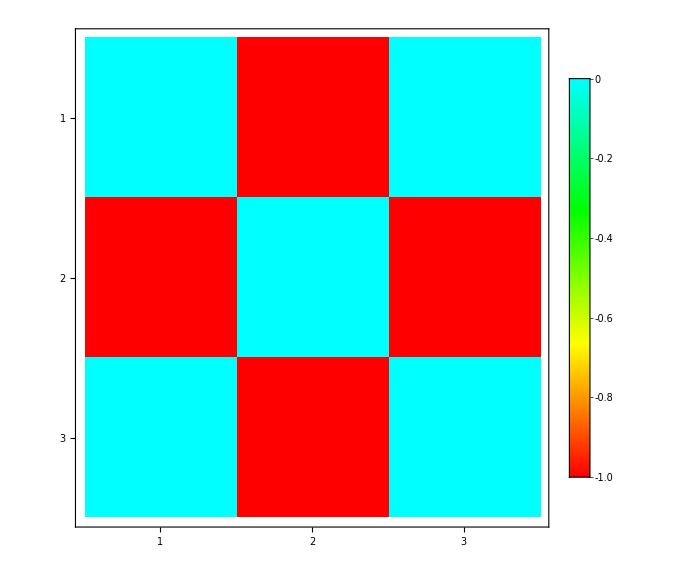

{{1.41421,-1.41421,1.33227×10^-15},{{-0.5,0.707107,-0.5},{0.5,0.707107,0.5},{0.707107,-7.85046×10^-16,-0.707107}}}

Energias Numericas

(1.41421
-1.41421
1.33227×10^-15)

(0. | -1. t1 | 0.
-1. t1 | 0. | -1. t1
0. | -1. t1 | 0.)

Energias Exactas

{{En→0.},{En→-1.41421 t1},{En→1.41421 t1}}

```mathematica
(********************* ----- HAMILTONIANO en Espacio de Estados ----- *********************)


HEdoBase=Table[Table[  0.  ,{i,1,NEdos,1}],{j,1,NEdos,1}];



(* NO DIAGONAL:  Transicion entre sitios*)

(*Transporte entre sitios*)
Base[[1]];
Base[[1+1]];
Base[[1]]+UnitVector[6,1] ;    (*   Notacion:  Subscript[b, n+1]^† Subscript[b, n] {n;...} = √1 √(0+1){0,...,0,1-1,0+1,...,0;...} = {n+1;...} *)


Do[  Do[  HEdoBase[[i,i+1]]=t  ,{i,    1 + 1*NZigzag*(j-1)  ,   1* (    NZigzag-1 +(j-1)*NZigzag    )     ,1}]  , {j,1,NArmchair,1} ]   (*Para interacciones entre filas  {n;...} y {n+1;...} en direccion zigzag *)


Do[  Do[  HEdoBase[[    i+1*(j-1),   i+1*(j-1+NZigzag)  ]]=t  ,{i,    1  ,   1    ,1}]  , {j,1,    (NArmchair-1)*NZigzag     ,2} ]   (*Para interacciones entre filas  {n;...} y {n+1;...} en direccion zigzag *)




HEdoBase  =(HEdoBase+ConjugateTranspose[HEdoBase]);
(*** CASO SIMPLE: Cadena de 3 atomos ***)
HEdoBase=HEdoBase[[1;;3,1;;3]];
NEdos=3;
(**)



HEdoBase // MatrixForm;
MatrixPlot[HEdoBase ,PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]


(*  Solución Numerica   *)
{eval,evec}=Eigensystem[HEdoBase ]

Print[     Style["Energias Numericas ",18,Bold,Purple]      ]
Style[    MatrixForm[  eval  ]   ,{Medium,Bold,Purple}]



(*  Solución Exacta:    Usa el mismo hamiltoniano de interacción   *)

t1*HEdoBase   // MatrixForm

Print[     Style["Energias Exactas ",18,Bold,Purple]      ]
Quiet[        Solve[   Det[           t1*HEdoBase-En*IdentityMatrix[   Round[NEdos]    ]          ]==0    ,En]          ]

(*Eigenfunction*)
```

```mathematica
(********************* ----- HAMILTONIANO en Espacio Real ----- *********************)

(*Para este problema simplificado queda identico*)

HReal = HEdoBase ;
HEdoBase // MatrixForm;
MatrixPlot[HEdoBase ,PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]


(* Para usar Green se requiere el Hamiltoniano discretiado (Matriz) en el espacio Real *)


(* Con Green obtendremos observables en función de la energía *)
Energia=En*IdentityMatrix[   Round[NEdos]    ];


(* Se ingresa las posiciones atomicas que actuaran de Fuente y Drenante *)
PosicionFuente={   1.   };
PosicionDrentante={3.   };

PosicionFuente=  Table   [    Round[{PosicionFuente[[i]] , PosicionFuente[[i]] }]    ,{i,1, Length[PosicionFuente],1}];              (* Genera las posiciones correspondientes a la matriz *)
PosicionDrentante=  Table   [    Round[{PosicionDrentante[[i]] , PosicionDrentante[[i]] }]    ,{i,1, Length[PosicionDrentante],1}];

(* Matrices de Autoenergías *)
SigmaFuente=-ⅈ *tF *SparseArray[{        PosicionFuente->Table[1. , {i,1, Length[PosicionFuente],1} ]        },{NEdos,NEdos}];
SigmaDrenante= -ⅈ*tD*SparseArray[{        PosicionDrentante->Table[1. , {i,1, Length[PosicionDrentante],1} ]        },{NEdos,NEdos}];


Energia  -  t1*HEdoBase   - SigmaFuente  -  SigmaDrenante    // MatrixForm
```

-Graphics-

((0.+0. ⅈ)+En+(0.+1. ⅈ) tF | (0.+0. ⅈ)+1. t1 | 0.+0. ⅈ
(0.+0. ⅈ)+1. t1 | (0.+0. ⅈ)+En | (0.+0. ⅈ)+1. t1
0.+0. ⅈ | (0.+0. ⅈ)+1. t1 | (0.+0. ⅈ)+En+(0.+1. ⅈ) tD)

Función de Transmisión

-((((0.+0. ⅈ)+1. t1^2) ((0.+0. ⅈ)+1. Conjugate[t1]^2) ((0.-1. ⅈ) tD-(0.+1. ⅈ) Conjugate[tD]) ((0.-1. ⅈ) tF-(0.+1. ⅈ) Conjugate[tF]))/(((0.+0. ⅈ)+En^3-2. En t1^2+(0.+1. ⅈ) En^2 tD-(0.+1. ⅈ) t1^2 tD+(0.+1. ⅈ) En^2 tF-(0.+1. ⅈ) t1^2 tF-(1.+0. ⅈ) En tD tF) ((0.+0. ⅈ)+Conjugate[En]^3+Conjugate[-2. En t1^2+(0.+1. ⅈ) En^2 tD-(0.+1. ⅈ) t1^2 tD+(0.+1. ⅈ) En^2 tF-(0.+1. ⅈ) t1^2 tF-(1.+0. ⅈ) En tD tF])))

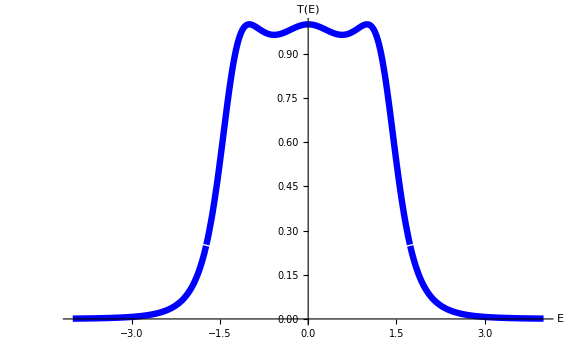

DOS

(2 ⅈ (((-1.+0. ⅈ)+(0.+1. ⅈ) En+En^2)/((0.-2. ⅈ)-(3.+0. ⅈ) En+(0.+2. ⅈ) En^2+En^3)-((-1.+0. ⅈ)-(0.+1. ⅈ) Conjugate[En]+Conjugate[En]^2)/((0.+2. ⅈ)-(3.+0. ⅈ) Conjugate[En]-(0.+2. ⅈ) Conjugate[En]^2+Conjugate[En]^3))+ⅈ (((-1.+0. ⅈ)+(0.+2. ⅈ) En+En^2)/((0.-2. ⅈ)-(3.+0. ⅈ) En+(0.+2. ⅈ) En^2+En^3)-((-1.+0. ⅈ)-(0.+2. ⅈ) Conjugate[En]+Conjugate[En]^2)/((0.+2. ⅈ)-(3.+0. ⅈ) Conjugate[En]-(0.+2. ⅈ) Conjugate[En]^2+Conjugate[En]^3)))/(2 π)

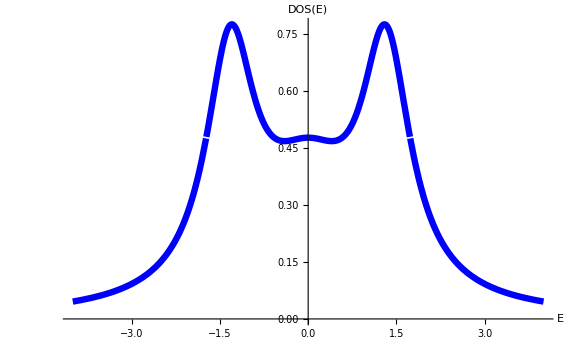

LDOS

((ⅈ (((-1.+0. ⅈ)+(0.+1. ⅈ) En+En^2)/((0.-2. ⅈ)-(3.+0. ⅈ) En+(0.+2. ⅈ) En^2+En^3)-((-1.+0. ⅈ)-(0.+1. ⅈ) Conjugate[En]+Conjugate[En]^2)/((0.+2. ⅈ)-(3.+0. ⅈ) Conjugate[En]-(0.+2. ⅈ) Conjugate[En]^2+Conjugate[En]^3)))/(2 π)
(ⅈ (((-1.+0. ⅈ)+(0.+2. ⅈ) En+En^2)/((0.-2. ⅈ)-(3.+0. ⅈ) En+(0.+2. ⅈ) En^2+En^3)-((-1.+0. ⅈ)-(0.+2. ⅈ) Conjugate[En]+Conjugate[En]^2)/((0.+2. ⅈ)-(3.+0. ⅈ) Conjugate[En]-(0.+2. ⅈ) Conjugate[En]^2+Conjugate[En]^3)))/(2 π)
(ⅈ (((-1.+0. ⅈ)+(0.+1. ⅈ) En+En^2)/((0.-2. ⅈ)-(3.+0. ⅈ) En+(0.+2. ⅈ) En^2+En^3)-((-1.+0. ⅈ)-(0.+1. ⅈ) Conjugate[En]+Conjugate[En]^2)/((0.+2. ⅈ)-(3.+0. ⅈ) Conjugate[En]-(0.+2. ⅈ) Conjugate[En]^2+Conjugate[En]^3)))/(2 π))

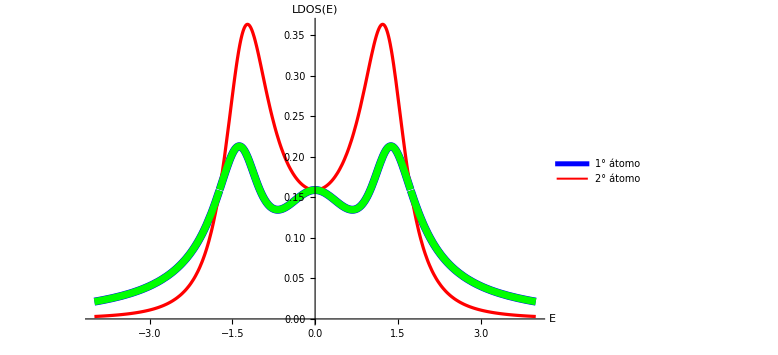

```mathematica
(*Broadening Matrix*)
GammaFuente = ⅈ*(  SigmaFuente -ConjugateTranspose[  SigmaFuente ]);
GammaDrenante= ⅈ*(  SigmaDrenante -ConjugateTranspose[  SigmaDrenante ]);



(*Funcion de Green del Nanosistema*)
FGreenE=Inverse[Energia  -  t1*HEdoBase   - SigmaFuente  -  SigmaDrenante ];






(*Funcion de Transmision*)
Print[     Style["Función de Transmisión",18,Bold,Purple]      ]
FTranmisionE=Tr[     GammaDrenante.FGreenE.GammaFuente.ConjugateTranspose[   FGreenE  ]     ]


tF=1.;
tD=1.;
t1=1.;


Plot[     FTranmisionE     ,{En,-4.,4.},PlotStyle->{{Thickness[0.008],Blue}},LabelStyle->{14,Black},AxesLabel->{"E" ,"T(E)"}, ImageSize->Large]




(*Función Espectral*)
A=ⅈ*(  FGreenE  -  ConjugateTranspose[  FGreenE  ]  );



(*DOS: Densidad de Estados*)
Print[     Style["DOS",18,Bold,Purple]      ]
DOS=Tr[  A  ]/(2*π)
Plot[     DOS     ,{En,-4.,4.},PlotStyle->{{Thickness[0.008],Blue}},LabelStyle->{14,Black},AxesLabel->{"E" ,"DOS(E)"}, ImageSize->Large]


(*LDOS: Densidad Local de Estados*)
Print[     Style["LDOS",18,Bold,Purple]      ]
LDOS=Diagonal[  A ]/(2*π);     (*Los elementos de la Diagonal de A *)
LDOS   //MatrixForm
Plot[     LDOS     ,{En,-4.,4.},PlotStyle->{{Thickness[0.010],Blue},{Thickness[0.004],Red},{Thickness[0.009],Green},{Thickness[0.005],Orange},{Thickness[0.002],Yellow},{Thickness[0.004],Pink}},LabelStyle->{14,Black},AxesLabel->{"E" ,"LDOS(E)"}, ImageSize->Large   ,  PlotLegends->{"1° átomo","2° átomo"}]
```

```mathematica
(*  Solución Numerica   *)
{eval,evec}=Eigensystem[HEdoBase  + SigmaFuente  +  SigmaDrenante]

Print[     Style["Energias Numericas ",18,Bold,Purple]      ]
Style[    MatrixForm[  eval  ]   ,{Medium,Bold,Purple}]
```

{{1.32288-0.5 ⅈ,-1.32288-0.5 ⅈ,-2.76743×10^-17-1. ⅈ},{{-0.467707+0.176777 ⅈ,0.707107+0. ⅈ,-0.467707+0.176777 ⅈ},{0.467707+0.176777 ⅈ,0.707107+0. ⅈ,0.467707+0.176777 ⅈ},{-0.707107-6.78586×10^-16 ⅈ,-3.22151×10^-16+2.33898×10^-16 ⅈ,0.707107+0. ⅈ}}}

Energias Numericas

(1.32288-0.5 ⅈ
-1.32288-0.5 ⅈ
-2.76743×10^-17-1. ⅈ)

LDOS

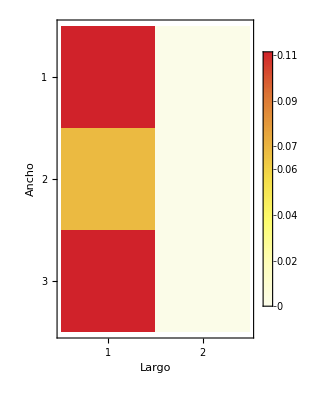

```mathematica
(*LDOS en Espacio REAL*)
Print[     Style["LDOS",18,Bold,Purple]      ]
En=-2.;

LDOSRealMatrix=SparseArray[  {{i_,i_}->0.},{NZigzag,NArmchair}  ];
Do[       LDOSRealMatrix [[       Mod[ i,NZigzag,1.]  ,   1.+IntegerPart[   (i-1)/NZigzag  ]   ]]=Re[  LDOS [[i]]  ]      ,   {i,1,NEdos,1.}];

MatrixPlot[     LDOSRealMatrix    ,PlotTheme->"Detailed",ColorFunction->"TemperatureMap",FrameLabel->{{"Largo",HoldForm["=E  "]En},{"Ancho",None}}]
```

Corriente Total

0.

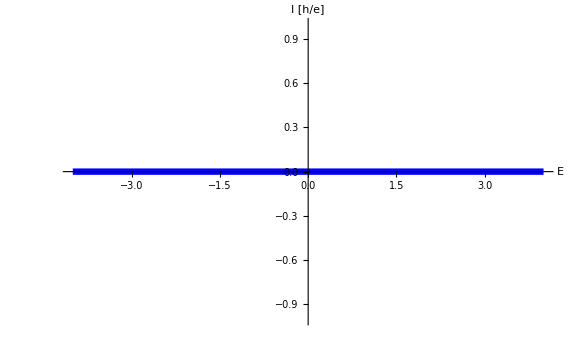

(0. | 2.77556×10^-17 | 0.
-2.77556×10^-17 | 0. | -2.77556×10^-17
0. | 2.77556×10^-17 | 0.)

La corriente total entre sitios 1-2: 2.77556×10^-17

La corriente total entre sitios 2-3: -2.77556×10^-17

```mathematica
(********** -------- Corriente -------- **********)
Print[     Style["Corriente Total",18,Bold,Purple]      ]
fFermi2=1;           (*Suponiendo Funciones de Fermi iguales a 1*)
SigmaDispersiva=GammaDrenante+GammaFuente;         (*Energías de Dispersión, In-Scattering*)
FGreenInE=  FGreenE.  SigmaDispersiva.  ConjugateTranspose[   FGreenE  ];        (*Funcion de Green de Dispersión*)
IVal=Im[  2*FGreenInE*fFermi2  ];      (*Matrices con los valores de las corrientes*)
ITotal=Tr[  IVal  ]     (*Corriente Total en Función de la Energía: Unidades (h/e)*)

Plot[     ITotal     ,{En,-4.,4.},PlotStyle->{{Thickness[0.008],Blue}},LabelStyle->{14,Black},AxesLabel->{"E" ,"I [h/e]"}, ImageSize->Large]

En=2.;
 Style[MatrixForm[ IVal ],{Large,Bold,Purple}]

Print[ Style[ "La corriente total entre sitios 1-2: ",{Large,Bold,Purple}] ,Style[ IVal[[1,2]] ,{Large,Bold,Purple}]]
Print[ Style[ "La corriente total entre sitios 2-3: ",{Large,Bold,Purple}] ,Style[ IVal[[2,3]] ,{Large,Bold,Purple}]]
Clear[En]
```

Corriente Total

Im[(4.+0. ⅈ)/(((0.-2. ⅈ)-(3.+0. ⅈ) En+(0.+2. ⅈ) En^2+En^3) ((0.+2. ⅈ)-(3.+0. ⅈ) Conjugate[En]-(0.+2. ⅈ) Conjugate[En]^2+Conjugate[En]^3))]+Im[((4.+0. ⅈ) ((0.-1. ⅈ)-1. En) ((0.+1. ⅈ)-1. Conjugate[En]))/(((0.-2. ⅈ)-(3.+0. ⅈ) En+(0.+2. ⅈ) En^2+En^3) ((0.+2. ⅈ)-(3.+0. ⅈ) Conjugate[En]-(0.+2. ⅈ) Conjugate[En]^2+Conjugate[En]^3))]+2 (0.+Im[((2.+0. ⅈ) ((-1.+0. ⅈ)+(0.+1. ⅈ) En+En^2) ((-1.+0. ⅈ)-(0.+1. ⅈ) Conjugate[En]+Conjugate[En]^2))/(((0.-2. ⅈ)-(3.+0. ⅈ) En+(0.+2. ⅈ) En^2+En^3) ((0.+2. ⅈ)-(3.+0. ⅈ) Conjugate[En]-(0.+2. ⅈ) Conjugate[En]^2+Conjugate[En]^3))])

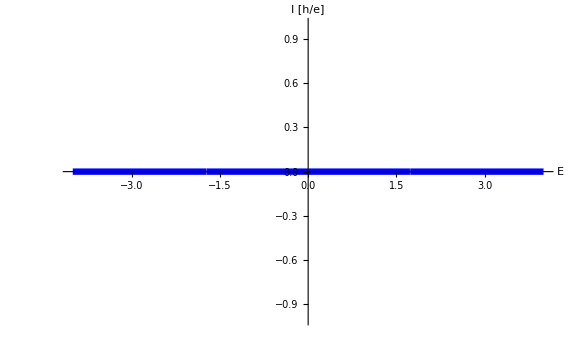

(0. | 0.1 | -0.2
-0.1 | 0. | 0.1
0.2 | -0.1 | 0.)

La corriente local drenante entre sitios 1-2: 0.1

La corriente local drenante entre sitios 2-3: 0.1

```mathematica
(********** -------- Corriente -------- **********)
Print[     Style["Corriente Total",18,Bold,Purple]      ]
fFermi2=1;           (*Suponiendo Funciones de Fermi iguales a 1*)
SigmaDispersiva=GammaDrenante;         (*Energías de Dispersión, In-Scattering*)
FGreenInE=  FGreenE.  SigmaDispersiva.  ConjugateTranspose[   FGreenE  ];        (*Funcion de Green de Dispersión*)
IVal=Im[  2*FGreenInE*fFermi2  ];      (*Matrices con los valores de las corrientes*)
ITotal=Tr[  IVal  ]     (*Corriente Total en Función de la Energía: Unidades (h/e)*)

Plot[     ITotal     ,{En,-4.,4.},PlotStyle->{{Thickness[0.008],Blue}},LabelStyle->{14,Black},AxesLabel->{"E" ,"I [h/e]"}, ImageSize->Large]

En=2.;
 Style[MatrixForm[ IVal ],{Large,Bold,Purple}]

Print[ Style[ "La corriente local drenante entre sitios 1-2: ",{Large,Bold,Purple}] ,Style[ IVal[[1,2]] ,{Large,Bold,Purple}]]
Print[ Style[ "La corriente local drenante entre sitios 2-3: ",{Large,Bold,Purple}] ,Style[ IVal[[2,3]] ,{Large,Bold,Purple}]]
Clear[En]
```